# FC: Pearson on Neural Data

```mathematica
SetDirectory[NotebookDirectory[]];
cd=ColorData[97,"ColorList"];
dir ="../AnalysisData/best_categ_pass_agent/";
```

```mathematica
aa=Flatten[Import[StringJoin[dir,"fc_corr_A_avoid.dat"]]];
ac=Flatten[Import[StringJoin[dir,"fc_corr_A_pass.dat"]]];
ba=Flatten[Import[StringJoin[dir,"fc_corr_B_avoid.dat"]]];
bc=Flatten[Import[StringJoin[dir,"fc_corr_B_catch.dat"]]];
```

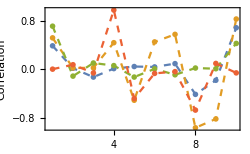

SubtaskMIe.eps

```mathematica
ListLinePlot[{ba,bc,aa,ac},PlotMarkers->{●},PlotStyle->Dashed,PlotRange->All,Frame->True,ImageSize->250,FrameLabel->{"Neuron Pairs","Correlation"}]
Export["SubtaskMIe.eps",%]
```

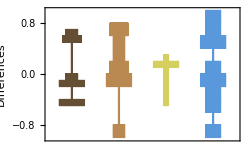

SubtaskCosFC_hist.eps

```mathematica
DistributionChart[{ba-bc,aa-ac,ba-aa,bc-ac},ChartStyle->"SouthwestColors",ChartElementFunction->"HistogramDensity",PlotRange->All,FrameLabel->{"","Differences"},Frame->True,ImageSize->250]
Export["SubtaskCosFC_hist.eps",%]
```

```mathematica
{CosineDistance[ba,bc],CosineDistance[aa,ac],CosineDistance[ba,aa],CosineDistance[bc,ac]}
```

{0.21416237519286077,0.933454253200114822,0.33305536466233644,0.529353420054421895}

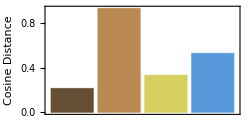

SubtaskCosFC.eps

```mathematica
BarChart[{CosineDistance[ba,bc],CosineDistance[aa,ac],CosineDistance[ba,aa],CosineDistance[bc,ac]},ChartStyle->"SouthwestColors",FrameLabel->{"","Cosine Distance"},AspectRatio->1/2,ChartStyle->{Black,Gray},PlotRange->{{0.5,4.5},Automatic},Frame->True,ImageSize->250]
Export["SubtaskCosFC.eps",%]
```

```mathematica
{EuclideanDistance[ba,bc],EuclideanDistance[aa,ac],EuclideanDistance[ba,aa],EuclideanDistance[bc,ac],EuclideanDistance[ba,ac],EuclideanDistance[bc,aa]}
```

{1.2990355195500064,1.51367327519719448,0.735576115263650184,1.7213432648094396,1.4563547437387294,1.6868205106775525}

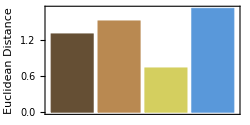

SubtaskEucFC_NA.eps

```mathematica
BarChart[{EuclideanDistance[ba,bc],EuclideanDistance[aa,ac],EuclideanDistance[ba,aa],EuclideanDistance[bc,ac]},ChartStyle->"SouthwestColors",FrameLabel->{"","Euclidean Distance"},AspectRatio->1/2,ChartStyle->{Black,Gray},PlotRange->{{0.5,4.5},All},Frame->True,ImageSize->250]
Export["SubtaskEucFC_NA.eps",%]
```

# FC: Pearson on MI

```mathematica
SetDirectory[NotebookDirectory[]];
cd=ColorData[97,"ColorList"];
dir ="../AnalysisData/best_categ_pass_agent/";
```

```mathematica
aa=Flatten[Import[StringJoin[dir,"fc_corr_mi_A_avoid.dat"]]];
ac=Flatten[Import[StringJoin[dir,"fc_corr_mi_A_pass.dat"]]];
ba=Flatten[Import[StringJoin[dir,"fc_corr_mi_B_avoid.dat"]]];
bc=Flatten[Import[StringJoin[dir,"fc_corr_mi_B_catch.dat"]]];
```

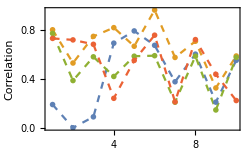

SubtaskMIe.eps

```mathematica
ListLinePlot[{ba,bc,aa,ac},PlotMarkers->{●},PlotStyle->Dashed,PlotRange->All,Frame->True,ImageSize->250,FrameLabel->{"Neuron Pairs","Correlation"}]
Export["SubtaskMIe.eps",%]
```

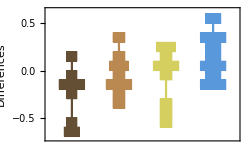

SubtaskCosFC_hist.eps

```mathematica
DistributionChart[{ba-bc,aa-ac,ba-aa,bc-ac},ChartStyle->"SouthwestColors",ChartElementFunction->"HistogramDensity",PlotRange->All,FrameLabel->{"","Differences"},Frame->True,ImageSize->250]
Export["SubtaskCosFC_hist.eps",%]
```

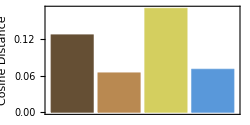

SubtaskCosFC.eps

```mathematica
BarChart[{CosineDistance[ba,bc],CosineDistance[aa,ac],CosineDistance[ba,aa],CosineDistance[bc,ac]},ChartStyle->"SouthwestColors",FrameLabel->{"","Cosine Distance"},AspectRatio->1/2,ChartStyle->{Black,Gray},PlotRange->{{0.5,4.5},Automatic},Frame->True,ImageSize->250]
Export["SubtaskCosFC.eps",%]
```

```mathematica
{EuclideanDistance[ba,bc],EuclideanDistance[aa,ac],EuclideanDistance[ba,aa],EuclideanDistance[bc,ac],EuclideanDistance[ba,ac],EuclideanDistance[bc,aa]}
```

{1.12556,0.6416288822013887,0.940723,0.843207510886909,1.27641,0.7318403418902883}

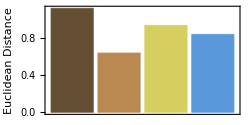

SubtaskEucFC_MI.eps

```mathematica
BarChart[{EuclideanDistance[ba,bc],EuclideanDistance[aa,ac],EuclideanDistance[ba,aa],EuclideanDistance[bc,ac]},ChartStyle->"SouthwestColors",FrameLabel->{"","Euclidean Distance"},AspectRatio->1/2,ChartStyle->{Black,Gray},PlotRange->{{0.5,4.5},All},Frame->True,ImageSize->250]
Export["SubtaskEucFC_MI.eps",%]
```